```mathematica
Clear["Global`*"]
```

### 関数

```mathematica
LoopMatrix[g_]:=(
FundLoop=FindFundamentalCycles[UndirectedGraph[g]];
RuleFundLoop=Table[EdgeRules[FundLoop[[i]]],{i,Length[FundLoop]}];
RuleRevFundLoop=Table[
EdgeRules[ReverseGraph[Graph[RuleFundLoop[[i]]]]],
{i,Length[FundLoop]}
];
Ruleg=EdgeRules[g];
Table[
Table[
If[MemberQ[RuleFundLoop[[j]],Ruleg[[i]]],1,0]+If[MemberQ[RuleRevFundLoop[[j]],Ruleg[[i]]],-1,0],
{i,EdgeCount[g]}
],
{j,Length[FundLoop]}]
)
```

```mathematica
VertexSortFromLoopEdgeList[LoopEdgeList_]:=(
UndirectedLoop=FindCycle[UndirectedGraph[LoopEdgeList]][[1]];
MinVertexNum=Min[VertexList[UndirectedLoop]];
VertexLoop={MinVertexNum};
For[j=1,Length[VertexLoop]≠ Length[UndirectedLoop],j++,
VertexLoop=Append[VertexLoop,UndirectedLoop[[FirstPosition[UndirectedLoop,VertexLoop[[j]]<->_][[1]],2]]]
];
VertexLoop=Append[VertexLoop,MinVertexNum]
)(* Vertex Sort From Loop Edge List ルールエッジで表現された巡回路から、頂点で表現された巡回路に直す *)
```

```mathematica
PartLoopByGreedyFromSort[SortList_]:=((* 入力として枝のコストの順位を与えられたときのGreedyを使った部分巡回路の構築 *)
EdgeSolution={};
EdgeProcess={Ruleg[[SortList[[1]]]]};
For[j=2,
EdgeSolution=={},
j++,
AppendEdgeProcess=Append[EdgeProcess,Ruleg[[SortList[[j]]]]];
If[Max[VertexDegree[AppendEdgeProcess]]≤2,
If[AcyclicGraphQ[UndirectedGraph[AppendEdgeProcess]],
EdgeProcess=AppendEdgeProcess,
EdgeSolution=AppendEdgeProcess
]
]
];
EdgeSolution=EdgeRules[FindCycle[UndirectedGraph[EdgeSolution]][[1]]];
VertexSortFromLoopEdgeList[EdgeSolution]
)
```

```mathematica
DelEle[list_,element_]:=Delete[list,FirstPosition[list,element]](* Delete Element *)
```

```mathematica
DelEleList[list_,elementlist_]:=Delete[list,Table[FirstPosition[list,i],{i,elementlist}]](* Delete Element *)
```

```mathematica
DelEdgeVertexList[edgelist_,vertexlist_]:=(
devl={};(* Variable of DelEdgeVertexList *)
Do[devl=Union[Position[edgelist,i].{{1},{0}},devl],{i,vertexlist}];
Delete[edgelist,devl]
)(* Delete Edge list from Vertex List 頂点リストに重複があってもUnionがあるのでOK *)
```

```mathematica
EdgeNum[Edge_]:=(
FirstPosition[EdgeRules[Gin],Edge,
FirstPosition[
EdgeRules[Gin],
EdgeRules[
ReverseGraph[{Edge}]
][[1]]
]
][[1]]
) (* Edge Number *)
```

```mathematica
EdgeNumList[Edge_]:=Table[EdgeNum[Edge[[i]]],{i,Length[Edge]}] (* Edge Number List *)
```

```mathematica
EdgeD[Edge_]:=PD[[EdgeNum[Edge]]](* Edge Distance *)
```

```mathematica
EdgeDList[Edge_]:=PD[[EdgeNumList[Edge]]](* Edge Distance *)
```

```mathematica
EdgeReconst[Edge1_,Side1_,Edge2_,Side2_]:=VertexList[{Edge1}][[Side1]]->VertexList[{Edge2}][[Side2]](* Edge Reconstraction ２つの枝のそれぞれ片方の頂点を使って枝を再構成する *)
```

```mathematica
RestVertex[PartLoop_]:=Delete[VertexList[Gin],Table[{VertexList[PartLoop][[i]]},{i,Length[VertexList[PartLoop]]}]]
```

```mathematica
TriTourDiff[Edge_,Vertex_]:=(
EdgeD[VertexList[{Edge}][[1]]->Vertex]+EdgeD[VertexList[{Edge}][[2]]->Vertex]-EdgeD[Edge]
)(* Triangle Tour Difference *)
```

```mathematica
TriTourDiffList[PartLoop_,Vertex_]:=Table[TriTourDiff[PartLoop[[i]],Vertex],{i,Length[PartLoop]}]
```

```mathematica
MinTriTourDiffPosition[PartLoop_,Vertex_]:=(
FirstPosition[TriTourDiffList[PartLoop,Vertex],Min[TriTourDiffList[PartLoop,Vertex]]][[1]]
)
```

```mathematica
MinEdgeReconstPair[EdgePair_]:=(
ReconstEdgeD1=EdgeD[EdgeReconst[EdgePair[[1]],1,EdgePair[[2]],1]]+EdgeD[EdgeReconst[EdgePair[[1]],2,EdgePair[[2]],2]];
ReconstEdgeD2=EdgeD[EdgeReconst[EdgePair[[1]],1,EdgePair[[2]],2]]+EdgeD[EdgeReconst[EdgePair[[1]],2,EdgePair[[2]],1]];
If[
ReconstEdgeD1<ReconstEdgeD2,
{ReconstEdgeD1,{EdgeReconst[EdgePair[[1]],1,EdgePair[[2]],1],EdgeReconst[EdgePair[[1]],2,EdgePair[[2]],2]}},
{ReconstEdgeD2,{EdgeReconst[EdgePair[[1]],1,EdgePair[[2]],2],EdgeReconst[EdgePair[[1]],2,EdgePair[[2]],1]}}
]
)(* Minimum Edge Reconstraction Pair 枝ペアを再構成し、枝のコストが小さいほうのコストと枝ペアを出力 *)
```

```mathematica
SquareTourDiff[Edge1_,Edge2_]:=(
MinEdgeReconstPair[{Edge1,Edge2}][[1]]-EdgeD[Edge1]-EdgeD[Edge2]
)(* Square Tour Difference *)
```

```mathematica
SquareTourDiffList[PartLoop1_,PartLoop2_]:=Table[SquareTourDiff[i,j],{i,PartLoop1},{j,PartLoop2}]
```

```mathematica
MinSquareTourDiffEdgePair[PartLoop1_,PartLoop2_]:=(
PairNum=FirstPosition[SquareTourDiffList[PartLoop1,PartLoop2],Min[SquareTourDiffList[PartLoop1,PartLoop2]]];
{PartLoop1[[PairNum[[1]]]],PartLoop2[[PairNum[[2]]]]}
)(* 最小のスクエアツアとなるPartLoopの枝ペア *)
```

```mathematica
JoinPartLoop[PartLoop1_,PartLoop2_]:=Join[DelEleList[Join[PartLoop1,PartLoop2],MinSquareTourDiffEdgePair[PartLoop1,PartLoop2]],MinEdgeReconstPair[MinSquareTourDiffEdgePair[PartLoop1,PartLoop2]][[2]]]
```

```mathematica
PartLoopByNewUndirectedGreedyFromSort[SortList_]:=((* 枝の向きを考慮しない、入力として枝のコストの順位を与えられたときの新しいGreedyを使った部分巡回路の構築(コストは優先順位が高い順にソートされる) *)
EdgeSolution={};
For[i=3,Length[EdgeSolution]==0,i++,
EdgeSolution=FindCycle[
UndirectedGraph[EdgeList[Gout][[SortList[[Range[i]]]]]],
Infinity,All];
];
EdgeSolution=EdgeRules[EdgeSolution[[1]]];
VertexSortFromLoopEdgeList[EdgeSolution]
)
```

```mathematica
PartLoopByNewDirectedGreedyFromSort[SortList_]:=((* 枝の向きを考慮する、入力として枝のコストの順位を与えられたときの新しいGreedyを使った部分巡回路の構築(コストは優先順位が高い順にでソートされる) *)
EdgeSolution={};
For[i=3,Length[EdgeSolution]==0,i++,
EdgeSolution=FindCycle[
Graph[EdgeList[Gout][[SortList[[Range[i]]]]]],
Infinity,All];
];
EdgeSolution=EdgeRules[EdgeSolution[[1]]];
VertexSortFromLoopEdgeList[EdgeSolution]
)
```

```mathematica
RestEdgeSort[Edge_,Cost_]:=
EdgeNumList[DelEdgeVertexList[Ruleg,VertexList[Edge]]][[
Ordering[Cost[[
EdgeNumList[DelEdgeVertexList[Ruleg,VertexList[Edge]]
]]]]
]](* 残りの枝でのソート(与えられた枝をRulegから引いたエッジリストの中でのソート) *)
```

```mathematica
RestVertexMinCost[PartLoop_]:=Table[Min[TriTourDiffList[PartLoop,i]],{i,RestVertex[PartLoop]}](* 残りの頂点のそれぞれの追加コストが最小になる位置での追加コストのリスト *)
```

```mathematica
MinRestVertex[PartLoop_]:=RestVertex[PartLoop][[
FirstPosition[RestVertexMinCost[PartLoop],Min[RestVertexMinCost[PartLoop]]][[1]]
]](* 残りの頂点の中でも最小の追加コストとなる頂点 *)
```

```mathematica
LoopDelEdge[PartLoop_]:=PartLoop[[MinTriTourDiffPosition[PartLoop,MinRestVertex[PartLoop]]]](* 頂点を追加するときに削除すべき枝 *)
```

```mathematica
InsertVertexLoop[PartLoop_]:=EdgeRules[EdgeAdd[EdgeDelete[PartLoop,LoopDelEdge[PartLoop]],{VertexList[{LoopDelEdge[PartLoop]}][[1]]-> MinRestVertex[PartLoop],MinRestVertex[PartLoop]-> VertexList[{LoopDelEdge[PartLoop]}][[2]]}]](* １つの頂点を閉路に挿入したときの閉路の枝リスト *)
```

```mathematica
ContinuousInsertVertexLoop[PartLoop_]:=(
PartLoopSolution={PartLoop};
For[j=1,Min[RestVertexMinCost[PartLoopSolution[[-1]]]]≤0.5,
PartLoopSolution=Append[PartLoopSolution,InsertVertexLoop[PartLoopSolution[[-1]]]]
];
PartLoopSolution)(* 連続で１つの頂点を閉路に挿入したときの閉路の枝リスト *)
```

```mathematica
OutEdgeSortEdgeList[PartLoop_,Cost_]:=(
OutVertex=Table[If[!RegionMember[
Polygon[Pin[[VertexSortFromLoopEdgeList[PartLoop]]]],Pin[[i]]
],i],{i,Range[Length[Pin]]}]/.Null->Nothing;
EdgeExceptInner=DelEdgeVertexList[Ruleg,
DelEleList[
Table[If[RegionMember[
Polygon[Pin[[VertexSortFromLoopEdgeList[PartLoop]]]],Pin[[i]]
],i],{i,Range[Length[Pin]]}]/.Null->Nothing,
VertexList[PartLoop]]
];(* PartLoopの内側の頂点を除いた頂点で構成される枝リストの変数 *)
OutEdge={};(* OutEdge is Variable *)
Do[OutEdge=Union[EdgeExceptInner[[Flatten[Position[EdgeExceptInner,i].{{1},{0}}]]],OutEdge],{i,OutVertex}];
Ruleg[[EdgeNumList[OutEdge][[Ordering[Cost[[EdgeNumList[OutEdge]]]]]]]]
)(* 部分巡回路よりも外側の頂点を見つけ、それらの頂点を含む枝のコストソートをルールエッジリストで出力 *)
```

```mathematica
InsertDetachedEdge[PartLoop_,DetachedEdge_]:=Join[DelEleList[Append[PartLoop,DetachedEdge],{MinSquareTourDiffEdgePair[PartLoop,{DetachedEdge}][[1]]}],MinEdgeReconstPair[MinSquareTourDiffEdgePair[PartLoop,{DetachedEdge}]][[2]]](* PartLoopのどの頂点にも接していない枝を挿入 *)
```

```mathematica
EdgeLoopSide[PartLoop_,ContactEdge_]:=Intersection[VertexList[PartLoop],VertexList[{ContactEdge}]][[1]](* PartLoopに接する枝のPartLoop側の頂点 *)
```

```mathematica
EdgeRestSide[PartLoop_,ContactEdge_]:=DelEle[VertexList[{ContactEdge}],EdgeLoopSide[PartLoop,ContactEdge]][[1]](* PartLoopに接する枝のPartLoop側でない頂点 *)
```

```mathematica
DelEdgeContactEdge[PartLoop_,ContactEdge_]:=PartLoop[[MinTriTourDiffPosition[PartLoop,EdgeRestSide[PartLoop,ContactEdge]]]](* PartLoopに接する枝を挿入する際に削除すべき枝 *)
```

```mathematica
InsertContactEdge[PartLoop_,ContactEdge_]:=Join[DelEle[PartLoop,DelEdgeContactEdge[PartLoop,ContactEdge]],{ContactEdge,EdgeRestSide[PartLoop,ContactEdge]->DelEle[VertexList[{DelEdgeContactEdge[PartLoop,ContactEdge]}],EdgeLoopSide[PartLoop,ContactEdge]][[1]]}](* PartLoopの頂点に接する枝を挿入 *)
```

```mathematica
InsertEdge[PartLoop_,ContactEdge_]:=If[IntersectingQ[VertexList[PartLoop],VertexList[{ContactEdge}]],InsertContactEdge[PartLoop,ContactEdge],InsertDetachedEdge[PartLoop,ContactEdge]](* PartLoopの頂点に接する枝か否かを判定し、枝を挿入 *)
```

### 渦電流の計算

```mathematica
Pin={{9.74997,2.54783},{6.2203,5.81193},{3.71653,1.11667},{5.86331,1.22919},{6.16159,3.98391},{3.72481,2.50755},{8.04133,4.38989},{5.48575,7.2216},{6.52432,8.68946},{1.20419,0.93775}}(*Point input*)
```

{{9.74997,2.54783},{6.2203,5.81193},{3.71653,1.11667},{5.86331,1.22919},{6.16159,3.98391},{3.72481,2.50755},{8.04133,4.38989},{5.48575,7.2216},{6.52432,8.68946},{1.20419,0.93775}}

```mathematica
Gin=DirectedGraph[CompleteGraph[Length[Pin],VertexLabels->"Name",EdgeLabels->"Name"],"Acyclic"];
```

```mathematica
h=LoopMatrix[Gin];
PD=Table[
EuclideanDistance[
Pin[[ConnectedComponents[{EdgeRules[Gin][[i]]}][[1,1]]]],
Pin[[ConnectedComponents[{EdgeRules[Gin][[i]]}][[2,1]]]]
],
{i,Length[EdgeRules[Gin]]}];(* Point Distance *)
r=IdentityMatrix[Length[EdgeRules[Gin]]]PD;
s=Table[0,{i,Length[EdgeRules[Gin]]}];
FLP=Table[
Pin[[
ConnectedComponents[RuleFundLoop[[i]]][[1]]
]],
{i,Length[RuleFundLoop]}];(* Fundamental Loop Point *)
LoopSpin=Table[
If[(Append[FLP[[i,2]]-FLP[[i,1]],0]×Append[FLP[[i,3]]-FLP[[i,2]],0]).{0,0,1}>0,1,-1],
{i,Length[RuleFundLoop]}];(* 右回りならば負、左回りならば正 *)
FLA=Table[
Area[Polygon[
Pin[[ConnectedComponents[RuleFundLoop[[i]]][[1]]]]
]],
{i,Length[RuleFundLoop]}];(* Fundamental Loop Area *)
U=Table[LoopSpin[[i]]FLA[[i]],{i,Length[RuleFundLoop]}];(* 誘導起電力は右回りなら負、左回りなら正 *)
Curr=Transpose[h].Inverse[h.r.Transpose[h]].(h.s+U);(* 誘導起電力行列を考慮した電流を求める式 *)
```

```mathematica
Gout=Graph[Table[If[Curr[[i]]>0,
VertexList[{EdgeRules[Gin][[i]]}][[1]]->VertexList[{EdgeRules[Gin][[i]]}][[2]],
VertexList[{EdgeRules[Gin][[i]]}][[2]]->VertexList[{EdgeRules[Gin][[i]]}][[1]]
],{i,Length[EdgeRules[Gin]]}
]];(* 電流値の正負をグラフの向きに反映した出力グラフ *)
```

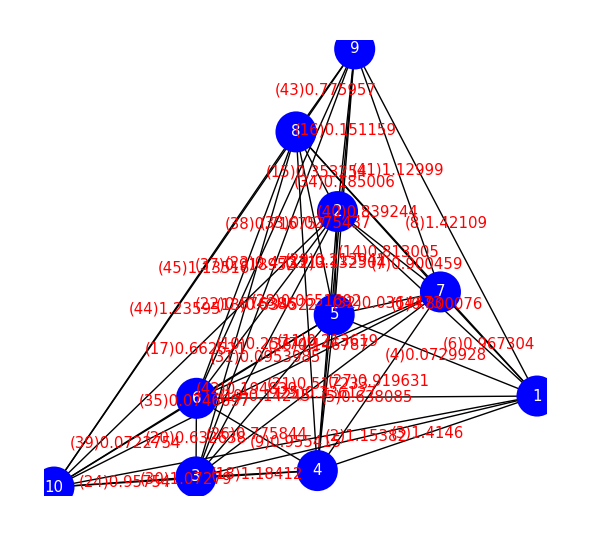

```mathematica
Graphics[{Thick,Arrowheads[{{Automatic,.8}}],Arrow[Table[
{Pin[[VertexList[{EdgeRules[Gout][[i]]}][[1]]]],Pin[[VertexList[{EdgeRules[Gout][[i]]}][[2]]]]},
{i,Length[EdgeRules[Gout]]}]],
Blue,PointSize[0.05],Point[Pin],White,Table[Text[Style[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}],
Red,Table[Text[Style["("<>TextString[i]<>")"<>TextString[Abs[Curr[[i]]]],FontSize->15],(Pin[[VertexList[{EdgeRules[Gin][[i]]}][[1]]]]+Pin[[VertexList[{EdgeRules[Gin][[i]]}][[2]]]])/2],
{i,Length[EdgeRules[Gin]]}]
}](* 電流値の正負をグラフの向きに反映した出力グラフの幾何学表示 *)
```

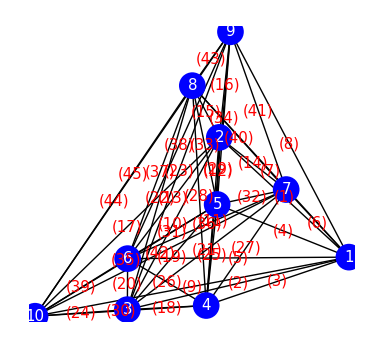

```mathematica
Graphics[{Thick,Arrowheads[{{Automatic,.8}}],Arrow[Table[
{Pin[[VertexList[{EdgeRules[Gout][[i]]}][[1]]]],Pin[[VertexList[{EdgeRules[Gout][[i]]}][[2]]]]},
{i,Length[EdgeRules[Gout]]}]],
Blue,PointSize[0.05],Point[Pin],White,Table[Text[Style[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}],
Red,Table[Text[Style["("<>TextString[i]<>")",FontSize->15],(Pin[[VertexList[{EdgeRules[Gin][[i]]}][[1]]]]+Pin[[VertexList[{EdgeRules[Gin][[i]]}][[2]]]])/2],
{i,Length[EdgeRules[Gin]]}]
}](* 電流値の正負をグラフの向きに反映した出力グラフの幾何学表示 *)
```

### TSPの解

```mathematica
Grid[{EdgeRules[Gin][[1;;10]],Range[10]},Frame->All]
Grid[{EdgeRules[Gin][[11;;20]],Range[11,20]},Frame->All]
Grid[{EdgeRules[Gin][[21;;30]],Range[21,30]},Frame->All]
Grid[{EdgeRules[Gin][[31;;40]],Range[31,40]},Frame->All]
Grid[{EdgeRules[Gin][[41;;45]],Range[41,45]},Frame->All]
```

1→2 | 1→3 | 1→4 | 1→5 | 1→6 | 1→7 | 1→8 | 1→9 | 1→10 | 2→3
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10

2→4 | 2→5 | 2→6 | 2→7 | 2→8 | 2→9 | 2→10 | 3→4 | 3→5 | 3→6
11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20

3→7 | 3→8 | 3→9 | 3→10 | 4→5 | 4→6 | 4→7 | 4→8 | 4→9 | 4→10
21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30

5→6 | 5→7 | 5→8 | 5→9 | 5→10 | 6→7 | 6→8 | 6→9 | 6→10 | 7→8
31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40

7→9 | 7→10 | 8→9 | 8→10 | 9→10
41 | 42 | 43 | 44 | 45

```mathematica
Curr
```

{0.800076,-1.15382,-1.4146,0.0729928,-0.638085,0.967304,0.900459,1.42109,-0.955415,0.257749,-0.213619,-0.132504,0.534522,-0.813005,0.353254,0.151159,0.662521,1.18412,0.14245,-0.632638,0.517233,-0.676386,-0.473313,-0.95754,0.336127,-0.775844,0.919631,-0.0651692,0.213941,-1.07279,0.0953985,0.0364473,0.0275437,0.185006,0.0746697,0.146787,-0.918952,-0.716757,0.0722754,0.839244,1.12999,-0.194839,-0.775957,1.23595,1.13516}

```mathematica
Reverse[Ordering[Abs[Curr]]](* 降順 *)
```

{8,3,44,18,2,45,41,30,6,24,9,27,37,7,40,14,1,43,26,38,22,17,5,20,13,21,23,15,25,10,29,11,42,34,16,36,19,12,31,35,4,39,28,32,33}

```mathematica
PDSort=Ordering[PD//N](* 昇順 *)
```

{20,15,43,12,32,18,14,26,6,24,25,31,16,39,33,19,40,27,4,3,13,41,11,30,36,34,1,37,10,21,35,28,5,2,7,22,38,8,17,29,44,42,23,9,45}

```mathematica
PDCurrCost=Abs[PD/Curr ]
```

{6.00891,5.37419,2.90135,52.9514,9.44278,2.59742,7.02613,4.88158,9.10194,20.6446,21.5178,13.803,7.74677,2.84191,4.4998,19.1424,10.557,1.81546,26.4529,2.19858,10.4862,9.39719,17.0639,2.63039,8.24337,3.21129,4.17391,92.1338,35.0073,4.3515,29.8655,52.7634,120.081,25.51,77.9231,32.0812,5.47604,9.46799,41.0856,4.54503,4.03485,39.3105,2.3173,6.15223,8.28229}

```mathematica
PDCurrCostSort=Ordering[PDCurrCost](* 昇順 *)
```

{18,20,43,6,24,14,3,26,41,27,30,15,40,8,2,37,1,44,7,13,25,45,9,22,5,38,21,17,12,23,16,10,11,34,19,31,36,29,42,39,32,4,35,28,33}

```mathematica
FindShortestTour[Pin]
Graphics[Line[Pin[[Last[%]]]]]
```

{26.8798,{1,7,9,8,2,5,6,10,3,4,1}}

-Graphics-

### 外側から挿入する電流コストによる新しいgreedyを用いた解法

```mathematica
CurrSort=Ordering[Abs[1/Curr]//N]
```

{8,3,44,18,2,45,41,30,6,24,9,27,37,7,40,14,1,43,26,38,22,17,5,20,13,21,23,15,25,10,29,11,42,34,16,36,19,12,31,35,4,39,28,32,33}

```mathematica
PartLoopByNewDirectedGreedyFromSort[CurrSort]
Graphics[Line[Pin[[%]]]]
```

{1,4,10,9,1}

-Graphics-

```mathematica
OutLoop1={EdgeSolution}
```

{{1→9,9→10,10→4,4→1}}

```mathematica
OutEdgeSortEdgeList[{1->9,9->10,10->4,4->1},Curr]
```

{8→9,4→8,1→8,8→10}

{{1→9,9→10,10→4,4→1},{1→9,10→4,4→1,8→9,8→10}}

{{1→9,10→4,4→1,8→9,8→10},{1→9,4→1,8→9,8→10,10→3,3→4},{4→1,8→9,8→10,10→3,3→4,1→7,7→9},{4→1,8→9,10→3,3→4,1→7,7→9,8→6,6→10},{4→1,8→9,10→3,3→4,1→7,8→6,6→10,7→2,2→9}}

{1,4,3,10,6,8,9,2,7,1}

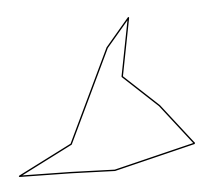

```mathematica
For[PartLoopCount=1,(oesel=OutEdgeSortEdgeList[OutLoop1[[PartLoopCount]],Curr])≠ {},PartLoopCount++,
OutLoop1=Append[OutLoop1,InsertEdge[OutLoop1[[PartLoopCount]],oesel[[1]]]]
]
OutLoop1
OutLoop2=ContinuousInsertVertexLoop[OutLoop1[[-1]]]
VertexSortFromLoopEdgeList[OutLoop2[[-1]]]
Graphics[line=Line[Pin[[%]]]]
```

{1,4,10,8,9,1}

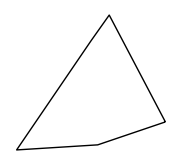

```mathematica
VertexSortFromLoopEdgeList[{1->9,10->4,4->1,8->9,8->10}]
Graphics[line=Line[Pin[[%]]]]
```

```mathematica
Show[-Graphics-,-Graphics-]
```

-Graphics-

```mathematica
RestVertexMinCost[{1->9,10->4,4->1,8->9,8->10}]
RestVertex[{1->9,10->4,4->1,8->9,8->10}]
```

{0.763958,0.000203459,1.52212,0.397842,0.134662}

{2,3,5,6,7}

{{1→9,9→10,10→4,4→1},{1→9,10→4,4→1,8→9,8→10},{1→9,10→4,4→1,8→9,8→10}}

{{1→9,10→4,4→1,8→9,8→10},{1→9,4→1,8→9,8→10,10→3,3→4},{4→1,8→9,8→10,10→3,3→4,1→7,7→9},{4→1,8→9,10→3,3→4,1→7,7→9,8→6,6→10}}

{1,4,3,10,6,8,9,7,1}

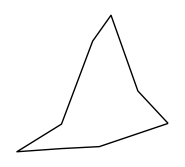

```mathematica
For[PartLoopCount=1,(oesel=OutEdgeSortEdgeList[OutLoop1[[PartLoopCount]],Curr])≠ {},PartLoopCount++,
OutLoop1=Append[OutLoop1,InsertEdge[OutLoop1[[PartLoopCount]],oesel[[1]]]]
]
OutLoop1
OutLoop2=ContinuousInsertVertexLoop[OutLoop1[[-1]]]
VertexSortFromLoopEdgeList[OutLoop2[[-1]]]
Graphics[line=Line[Pin[[%]]]]
```

### 外側から挿入する距離と電流コストによる新しいgreedyを用いた解法

{4,6,8,7,4}

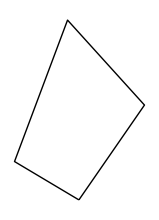

```mathematica
PartLoopByNewDirectedGreedyFromSort[PDCurrCostSort]
Graphics[Line[Pin[[%]]]]
```

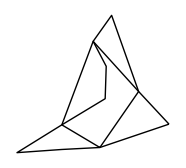

```mathematica
Show[-Graphics-,-Graphics-]
```

```mathematica
OutLoop1={EdgeSolution}
```

{{4→7,7→8,8→6,6→4}}

{{4→7,7→8,8→6,6→4},{4→7,7→8,8→6,3→4,3→6},{4→7,8→6,3→4,3→6,8→9,9→7},{8→6,3→4,3→6,8→9,9→7,1→7,1→4},{8→6,3→4,8→9,9→7,1→7,1→4,3→10,10→6}}

{{8→6,3→4,8→9,9→7,1→7,1→4,3→10,10→6},{8→6,3→4,8→9,1→7,1→4,3→10,10→6,9→2,2→7}}

{1,7,2,9,8,6,10,3,4,1}

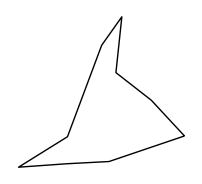

```mathematica
For[PartLoopCount=1,(oesel=OutEdgeSortEdgeList[OutLoop1[[PartLoopCount]],PDCurrCost])≠ {},PartLoopCount++,
OutLoop1=Append[OutLoop1,InsertEdge[OutLoop1[[PartLoopCount]],oesel[[1]]]]
]
OutLoop1
OutLoop2=ContinuousInsertVertexLoop[OutLoop1[[-1]]]
VertexSortFromLoopEdgeList[OutLoop2[[-1]]]
Graphics[line=Line[Pin[[%]]]]
```

```mathematica
Show[-Graphics-,-Graphics-]
```

-Graphics-

```mathematica
{1,7,9,8,2,5,6,10,3,4,1}
```

```mathematica
InsertVertexLoop[{8->6,3->4,8->9,1->7,1->4,3->10,10->6,9->2,2->7}]
```

{3→4,8→9,1→7,1→4,3→10,10→6,9→2,2→7,8→5,5→6}

{1,7,2,9,8,5,6,10,3,4,1}

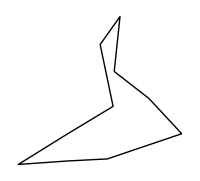

```mathematica
VertexSortFromLoopEdgeList[{3->4,8->9,1->7,1->4,3->10,10->6,9->2,2->7,8->5,5->6}]
Graphics[line=Line[Pin[[%]]]]
```

```mathematica
ArcLength[Line[Pin[[{1,7,2,9,8,5,6,10,3,4,1}]]]]
```

27.4134

{1,7,9,8,6,10,3,4,1}

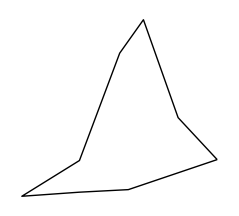

```mathematica
VertexSortFromLoopEdgeList[{8->6,3->4,8->9,9->7,1->7,1->4,3->10,10->6}]
Graphics[line=Line[Pin[[%]]]]
```

```mathematica
InsertDetachedEdge[{8->6,3->4,8->9,9->7,1->7,1->4,3->10,10->6},2->5]
```

{3→4,8→9,9→7,1→7,1→4,3→10,10→6,2→5,8→2,6→5}

{1,7,9,8,2,5,6,10,3,4,1}

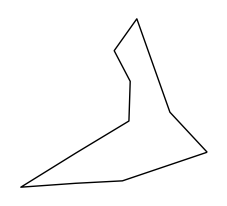

```mathematica
VertexSortFromLoopEdgeList[{3->4,8->9,9->7,1->7,1->4,3->10,10->6,2->5,8->2,6->5}]
Graphics[line=Line[Pin[[%]]]]
```

```mathematica
RestVertexMinCost[{8->6,3->4,8->9,9->7,1->7,1->4,3->10,10->6}]
RestVertex[{8->6,3->4,8->9,9->7,1->7,1->4,3->10,10->6}]
```

{0.644688,1.12439}

{2,5}

```mathematica
PD[[EdgeNum[2->5]]]
```

1.82896

```mathematica
ArcLength[Line[Pin[[{1,7,9,8,2,5,6,10,3,4,1}]]]]
```

26.8798

```mathematica
ArcLength[Line[Pin[[{1,7,2,9,8,6,10,3,4,1}]]]]
```

26.289